```mathematica
Needs["MaTeX`"];
texStyle={FontFamily->"Latin Modern Roman",FontSize-> 17};
SetOptions[MaTeX,FontSize-> 27];
SetOptions[$FrontEndSession,PrintingStyleEnvironment-> "Working"];
```

## Pi method normalized to saxion levels

```mathematica
dataPi=Import["/Users/z5278074/OneDrive - UNSW/AxionSimulations/PQsim/Output/Cores/Pi.txt","Table"]; 
a=dataPi[[All,1]];b=dataPi[[All,2]];c=dataPi[[All,3]];d=dataPi[[All,4]];
Pi01=Transpose[{a,b}];Pi05=Transpose[{a,c}];Pi1=Transpose[{a,d}];
one=Table[{x,1},{x,0,10,1}];
```

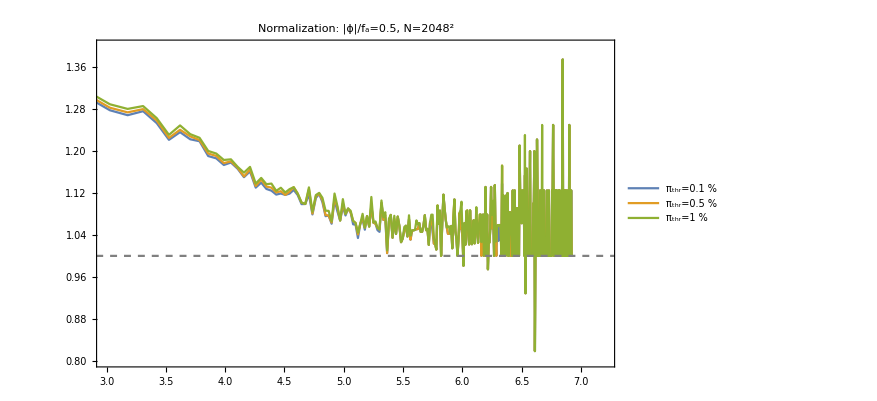

```mathematica
c1=ListPlot[{Pi01,Pi05,Pi1,one},PlotRange->{{3,7.2},{0.8,1.4}},Frame->True,Joined->True,PlotStyle->{,,,Directive[Gray,Dashed]},PlotLegends->Placed[LineLegend[{"π_thr=0.1 %","π_thr=0.5 %","π_thr=1 %"},LegendLayout->"Column"],{Left,Bottom}],ImageSize->650,BaseStyle->texStyle,FrameLabel->MaTeX/@{"\\kappa","\\text{Norm. cores}"},PlotLabel->"Normalization:  |ϕ|/f_a=0.5,    N=2048^2",LabelStyle->{texStyle,Gray}]
Export["/Users/z5278074/OneDrive - UNSW/AxionSimulations/PQsim/Output/Cores/Pi.pdf",c1];
```

```mathematica
(*Extend to multiple simulations*)
```